```mathematica
(*  3D plot *)
(* Subscript[ψ, nx,ny](x,y)=(2/L)sin(Subscript[n, x] πx/L)sin(Subscript[n, y] πy/L) *)
psi[x_,y_]:=2*Sin[nx*Pi*x]*Sin[ny*Pi*y];
Plot3D[psi[x,y]/.{nx->1,ny->1},{x,0,1},{y,0,1}]
```

-Graphics3D-

```mathematica
Plot3D[psi[x,y]/.{nx->1,ny->1},{x,0,1},{y,0,1},
AxesLabel->{"x","y","ψ"}]
```

-Graphics3D-

```mathematica
(* Probability density *)
```

```mathematica
Plot3D[(psi[x,y]/.{nx->2,ny->3})^2,{x,0,1},{y,0,1}]
```

-Graphics3D-

```mathematica
Plot3D[psi[x,y]/.{nx->2,ny->3},{x,0,1},{y,0,1},
AxesLabel->{"x","y","ψ"}]
```

-Graphics3D-

```mathematica
(* Amplitude goes plus and minus *)
```

```mathematica
(* Lake color is default color int 3D plot *)
```

```mathematica
Plot3D[(psi[x,y]/.{nx->2,ny->3})^2,{x,0,1},{y,0,1},
AxesLabel->{"x", "y","prob density"},
Mesh->None,
ColorFunction->"GrayTones"]
```

-Graphics3D-

```mathematica
(* Reduce the opacity *)
```

```mathematica
Plot3D[psi[x,y]/.{nx->2,ny->3},{x,0,1},{y,0,1},
AxesLabel->{"x","y","ψ"},
PlotStyle->Opacity[0.8]]
```

-Graphics3D-

```mathematica
Plot3D[psi[x,y]/.{nx->2,ny->3},{x,0,1},{y,0,1},
AxesLabel->{"x","y","ψ"},
Mesh->None,
PlotStyle->Directive[Pink, Specularity[White,50]],
ViewPoint->{4,2,4}]
```

-Graphics3D-

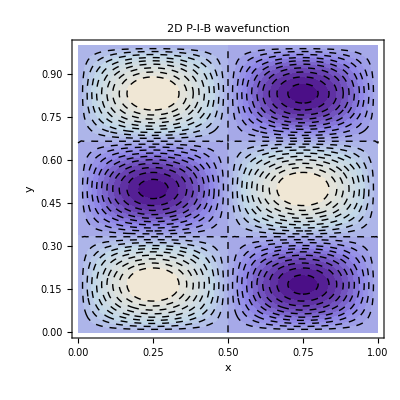

```mathematica
ContourPlot[psi[x,y]/.{nx->2,ny->3},{x,0,1},{y,0,1},
FrameLabel->{"x","y"},
Contours->20,
ContourStyle->Dashed,
PlotLabel->"2D P-I-B wavefunction"]
```

```mathematica
<<PlotLegends`
```

```mathematica
$Packages
```

{PlotLegends`,ResourceLocator`,DocumentationSearch`,GetFEKernelInit`,JLink`,PacletManager`,WebServices`,System`,Global`}

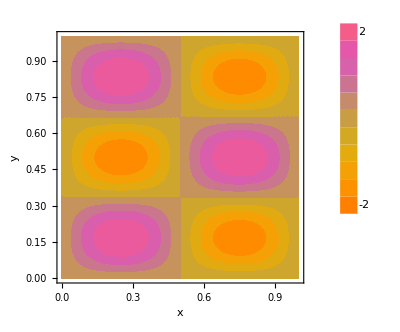

```mathematica
ShowLegend[ContourPlot[psi[x,y]/.{nx->2,ny->3},{x,0,1},{y,0,1},
FrameLabel->{"x","y"},
ColorFunction->"FruitPunchColors",
ContourStyle->None],
{ColorData["FruitPunchColors"][1-#1] &,11,"2","-2",
LegendPosition->{1.1,-0.4},
LegendShadow->None,
LegendSize->1.5}]
```

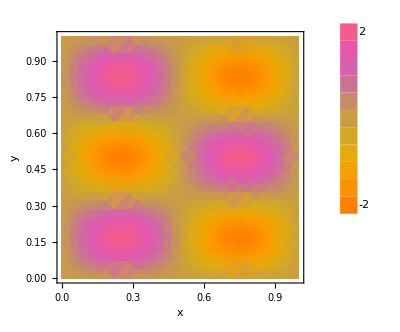

```mathematica
ShowLegend[DensityPlot[psi[x,y]/.{nx->2,ny->3},{x,0,1},{y,0,1},
FrameLabel->{"x","y"},
ColorFunction->"FruitPunchColors"],
{ColorData["FruitPunchColors"][1-#1] &,11,"2","-2",
LegendPosition->{1.1,-0.4},
LegendShadow->None,
LegendSize->1.5}]
```

```mathematica
2^5
```

32